```mathematica
DualDiagram[λ_] := Total /@ Transpose[
     (PadRight[#1, λ[[1]]] & ) /@ 
      (ConstantArray[1, #1] & ) /@ λ]; 
ToYD[stb_]:=Length/@stb;
CheckStandard[λT_] := 
   And @@ Flatten[{Table[λT[[a - 1,s]] < 
        λT[[a,s]], {a, 2, Length[λT]}, 
       {s, 1, Length[λT[[a]]]}], 
      Table[λT[[a,s - 1]] < λT[[a,s]], 
       {a, 1, Length[λT]}, {s, 2, 
        Length[λT[[a]]]}], Sort[Flatten[λT]] == 
       Range[Length[Flatten[λT]]], 
      ListQ /@ λT}]; 
ToTableau[path_]:=Block[{pr=path//Flatten,max},max=Max[pr];
Table[Position[pr,k]//Flatten,{k,max}]];
Quiet[Needs["Combinatorica`"]];
ToSYT[rigged_]:=ToTableau[kkrrec[ConstantArray[{1,1},Length[rigged[[1,1]]]],rigged[[2;;3]]]];
```

```mathematica
(*Importing a Matlab package allowing us to plot rigged configurations*)
Directory[];
SetDirectory["C:\\Users\\thoma\\OneDrive\\Dokument\\Uppsala\\Fysik\\Project_Bethe_ansatz\\VolinStringHypothesis\\StringHypothesis"];
<<RC.m;
ResetDirectory[];
```

```mathematica
Unprotect[M];
ClearAll[M];(* Unprotecting because of conflict with Combinatorica package *)
M[a_,s_,YD_]:=M[a,s,YD]=Total[YD]+a s-Total[YD[[1;;a]]]-Total[DualDiagram[YD][[1;;s]]];
YQa[0,0,YD_]:=u^Total[YD]+Sum[u^(Total[YD]-k)sym[k],{k,Len}];
YQa[a_,s_,YD_]:=u^M[a,s,YD]+Sum[c[a,s,k] u^(M[a,s,YD]-k),{k,M[a,s,YD]}];
YQθ[0,0,YD_]:=YQa[0,0,YD];
YQθ[a_,s_,YD_]:=Product[u-qθ[a,s,k],{k,1,M[a,s,YD]}];
QQrel[a_,s_,YD_]:=
CoefficientList[(YQa[a,s,YD]/.u->u+I/2)(YQa[a+1,s+1,YD]/.u->u-I/2)-(YQa[a,s,YD]/.u->u-I/2)(YQa[a+1,s+1,YD]/.u->u+I/2)-I(M[a,s,YD]-M[a+1,s+1,YD])YQa[a+1,s,YD]YQa[a,s+1,YD],u]//(#/.Complex[0,b_]:>b)&;
```

```mathematica
YQprod[a_,s_,YD_]:=Product[u-x[a,s,k],{k,1,M[a,s,YD]}];
coeff2root[YD_]:=Table[If[{a,s}!={0,0},Thread[CoefficientList[YQa[a,s,YD],u][[;;-2]]->CoefficientList[YQprod[a,s,YD],u][[;;-2]]],Nothing],{a,0,Length[YD]-1},{s,0,YD[[a+1]]-1}]//Flatten;
```

```mathematica
GenerateQsystem[λ_]:=Block[{},
((* Length of spin chain *)
Len=Total[λ];
(* domain of interest is the values of {a,s} for which we are going to check QQ relation with Q[a,s] in the top left corner (smallest a,s)
FullYoungDiagram - is maximal possible domain of interest*)
FullYoungDiagram=Block[{mm},Flatten@Table[mm[a,s],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}]/.mm->List];
DomainOfInterest=FullYoungDiagram;
(* comment below provides some example of non-standard DomainOfInterest *)
(*DomainOfInterest=Block[{mm},Flatten@Table[mm[a,s],{a,0,1},{s,0,1}]/.mm->List];*)
Allrel=Monitor[Table[If[MemberQ[DomainOfInterest,{a,s}]&&M[a,s,λ]>0,QQrel[a,s,λ],Nothing],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}],{a,s}]//Flatten;
(* vars have coefficients of all Q-functions *)
vars=Table[If[a+s==0,Nothing,c[a,s,k]],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1},{k,M[a,s,λ]}]//Flatten;
(* only those appearing in domain of interest *)
vars2=DeleteCases[Variables[Allrel],sym[_]];
)
];
```

```mathematica
initθrep[λT_] := initθrep[λT] = 
   Block[{kk, sd}, kk[_, _] = 0; sd[m_] := 
      (Select[#1, #1 <= m & ] & ) /@ λT; 
     If[CheckStandard[λT], 
      Sort[Flatten[Table[Table[If[True || 
            MemberQ[DomainOfInterest, {a2, s2}], 
           qθ[a2, s2, ++kk[a2, s2]] -> 
            Product[(Length[sd[λT[[a,s]]][[a3]]] + a - 
                s - a3)/(Length[sd[λT[[a,s]]][[a3]]] + 
                a - s - a3 + 1), {a3, 1, a2}]*
             Product[(DualDiagram[Length /@ sd[λT[[a,
                   s]]]][[s3]] + s - a - s3)/(
                DualDiagram[Length /@ sd[λT[[a,s]]]][[
                 s3]] + s - a - s3 + 1), {s3, 1, s2}]*
             θ[λT[[a,s]]], Nothing], {a2, 0, a - 1}, 
          {s2, 0, s - 1}], {a, 1, Length[λT]}, 
         {s, 1, Length[λT[[a]]]}]]], 
      Print["Not standard tableau"]; ]]
```

```mathematica
LargeΛExpansionUptdStart[λT_]:=Block[{λ,Len},λ=λT//ToYD;Len=Total[λ];
ΛinitθrepUptd=initθrep[λT]/.θ[i_]:>If[i==(λT//Max),Λ,0];  (*The set of  qθ for the initial λT will be used here*)
fsymrepUptd=Table[sym[n]->Expand@Coefficient[Product[u,{i,Len-1}](u-Λ),u,Len-n],{n,Len}];
ftransitUptd=Solve[(Table[If[a+s==0||Not@MemberQ[vars2,c[a,s,1]],Nothing,CoefficientList[YQa[a,s,λ]-(YQθ[a,s,λ]/.ΛinitθrepUptd),u]],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}]//Flatten)==0,vars2][[1]];
];

LargeΛExpansionUptdInterim[λTcurrent_,λTlast_,solninterim_]:=Block[{λcurrent,λlast,Len},λcurrent=λTcurrent//ToYD;λlast=λTlast//ToYD;Len=Total[λcurrent];
(*The set of  qθ for the current λT---having removed some boxes*)
ΛinitθrepUptd=initθrep[λTcurrent]/.θ[i_]:>If[i==(λTcurrent//Max),Λ,0]; 
fsymrepUptd=Table[sym[n]->Expand@Coefficient[Product[u,{i,Len-1}](u-Λ),u,Len-n],{n,Len}];
ftransitUptdInterim=Solve[(Table[If[a+s==0||Not@MemberQ[vars2,c[a,s,1]],Nothing,CoefficientList[YQa[a,s,λcurrent]-If[a<Position[λTcurrent,λTcurrent//Max][[1,1]]&&s<Position[λTcurrent,λTcurrent//Max][[1,2]],(u-Sum[qθ[a,s,k],{k,M[a,s,λcurrent]}])YQa[a,s,λlast]/.solninterim/.ΛinitθrepUptd,YQa[a,s,λlast]/.solninterim/.ΛinitθrepUptd],u]],{a,0,Length[λcurrent]-1},{s,0,λcurrent[[a+1]]-1}]//Flatten)==0,vars2][[1]];
];
```

```mathematica
varx=Table[If[{a,s}!={0,0},Thread[CoefficientList[YQa[a,s,{4,2,1}],u][[;;-2]]->CoefficientList[Product[u-x[a,s,k],{k,M[a,s,{4,2,1}]}],u][[;;-2]]],Nothing],{a,0,Length[{4,2,1}]-1},{s,0,{4,2,1}[[a+1]]-1}]//Flatten
```

{c[0,1,4]→x[0,1,1] x[0,1,2] x[0,1,3] x[0,1,4],c[0,1,3]→-x[0,1,1] x[0,1,2] x[0,1,3]-x[0,1,1] x[0,1,2] x[0,1,4]-x[0,1,1] x[0,1,3] x[0,1,4]-x[0,1,2] x[0,1,3] x[0,1,4],c[0,1,2]→x[0,1,1] x[0,1,2]+x[0,1,1] x[0,1,3]+x[0,1,2] x[0,1,3]+x[0,1,1] x[0,1,4]+x[0,1,2] x[0,1,4]+x[0,1,3] x[0,1,4],c[0,1,1]→-x[0,1,1]-x[0,1,2]-x[0,1,3]-x[0,1,4],c[0,2,2]→x[0,2,1] x[0,2,2],c[0,2,1]→-x[0,2,1]-x[0,2,2],c[0,3,1]→-x[0,3,1],c[1,0,3]→-x[1,0,1] x[1,0,2] x[1,0,3],c[1,0,2]→x[1,0,1] x[1,0,2]+x[1,0,1] x[1,0,3]+x[1,0,2] x[1,0,3],c[1,0,1]→-x[1,0,1]-x[1,0,2]-x[1,0,3],c[1,1,1]→-x[1,1,1],c[2,0,1]→-x[2,0,1]}

```mathematica
SYT=syts[[10]];
λTlist=Table[Select[MemberQ[Range[1,i],#]&]/@SYT/.{{}->Nothing},{i,Count[SYT[[1]]-Range[SYT[[1]]//Length],0],SYT//Max}][[2;;]]
```

{{{1,2},{3}},{{1,2},{3,4}},{{1,2,5},{3,4}},{{1,2,5},{3,4},{6}},{{1,2,5,7},{3,4},{6}}}

```mathematica
xsol=Table[If[{a,s}!={0,0},soll=NSolve[(YQa[a,s,{3,2,1}]/.testind[[-2,2,-1]])==0,u]//Flatten;Thread[Table[x[a,s,k],{k,Length@soll}]->(soll//Values)],Nothing],{a,0,Length[{3,2,1}]-1},{s,0,{3,2,1}[[a+1]]-1}]//Flatten
```

{x[0,1,1]→-0.510459501727978803838609502598384159389,x[0,1,2]→-0.0747542555869632174605875195138123592888,x[0,1,3]→0.223621891004553398191772946851766554318,x[0,2,1]→0.2383056820741863638158387337589486845323,x[1,0,1]→-0.481845143514616471656444402367436519995-0.506050731084853690959778962683211354208 ⅈ,x[1,0,2]→-0.481845143514616471656444402367436519995+0.506050731084853690959778962683211354208 ⅈ,x[1,0,3]→0.750041841802287058441943814292616368357,x[1,1,1]→-0.4793669262811120899956780592968559936948,x[2,0,1]→0.3369346294631481670270624163956037295823}

```mathematica
ΛinitθrepUptd
```

{qθ[0,0,1]→0,qθ[0,0,2]→0,qθ[0,0,3]→0,qθ[0,0,4]→Λ,qθ[0,0,5]→0,qθ[0,0,6]→0,qθ[0,0,7]→0,qθ[0,1,1]→0,qθ[0,1,2]→0,qθ[0,1,3]→(5 Λ)/6,qθ[0,1,4]→0,qθ[0,2,1]→0,qθ[0,2,2]→(5 Λ)/8,qθ[0,3,1]→(5 Λ)/16,qθ[1,0,1]→0,qθ[1,0,2]→0,qθ[1,0,3]→0,qθ[1,1,1]→0,qθ[2,0,1]→0}

```mathematica
ff=Allrel/.fsymrepUptd/.varx;
```

```mathematica
D[ff,{Variables[ff]/.(Λ->Nothing)}]/.xsol/.(x[0,1,4]->(5 Λ)/6)/.(x[0,2,2]->(5 Λ)/8)/.(Λ->0)//Chop
-D[ff,{Λ}]/.xsol/.(x[0,1,4]->(5 Λ)/6)/.(x[0,2,2]->(5 Λ)/8)/.(Λ->0)//Chop
```

{{0,0,0,0.018749999999999995960238465969195478285,0,0,0,0,0,0,1/64,0},{0.036731611296348780283859824461907632615,0.25082184088085422331377321349408096359,-0.083846889567793734849038943221130737103,0.21571511682650045628442786974518872711,0,0,0,0.01850357978407722348134702625850751131-0.019433110831250195282236394632005257204 ⅈ,0.01850357978407722348134702625850751131+0.019433110831250195282236394632005257204 ⅈ,-0.02499860535106325942686027750668415461,0,0},{0.35063213619154267227258914448584603054,-0.46962843491248959490172621902058628433,-1.3395915983386192596496624398700043622,-0.67499999999999997788072901797210965138,0,0,0,0.21476081101784712350725006009028134476-0.18521874879081394853010829771567452619 ⅈ,0.21476081101784712350725006009028134476+0.18521874879081394853010829771567452619 ⅈ,-0.32093372497612802049715864172003737627,-21/16,0},{-2.0092331178470190299976908967752298903,-2.7472892810576819643831842779390615765,-2.9719433788576934990751474255016337564,-2.876201557686672517633363029384848683,0,0,0,-0.68610046304728627914161627292509164466+1.1049616186437690517771159440499419523 ⅈ,-0.68610046304728627914161627292509164466-1.1049616186437690517771159440499419523 ⅈ,0.4720620307969494988391660579115624633,0,0},{-1.6984078793809120445264989091664146064,-1.7244807752653513696511290247127732978,-0.4281415416931228907281534821304262663,-1.4999999999999999987061197457550413442,0,0,0,-3.30653610342595918059522500120346890652+1.1794523645254122117150792320787641999 ⅈ,-3.30653610342595918059522500120346890652-1.1794523645254122117150792320787641999 ⅈ,4.4641024031913046712717524353963866066,35/4,0},{0.3886848588561342248385573786258148596,3.0029163357022277431066892771332456602,4.79317321525132743702085207532671914187,3.451441869224007047870214394216119816,0,0,0,0.56037100813630821793154798001150069599-3.03630438650912214575867377609926812525 ⅈ,0.56037100813630821793154798001150069599+3.03630438650912214575867377609926812525 ⅈ,7.9516929200377293985218772799718180261,0,0},{6,6,6,6,0,0,0,6,6,6,-7,0},{0.2667166879949944155281978101087587948015,0.364149919057652713094449413905920112842,0.21184097994103278034567083307526867446,0.342707586993679908968318057089947582104,0,-0.456943449324906518076945458673534145655,0,0,0,0,0,0},{0.297735270835180361462370854675908390058,-0.573675221446850811293673111493235210142,-1.17042751462988404259839404422439303735,-0.723183732620777246214848150520859928719,1.917467705124448359982712237187423974779,0.96424497682770290471935730215162923665,0,0,0,0,-0.9532227282967454552633549350357947381292,0},{-3,-3,-3,-3,4,4,0,0,0,0,4,0},{0,0,0,0,-1,-1,2,0,0,0,0,0},{0,0,0,0,0,0,0,0.26819669828767058678549941192517984836+0.506050731084853690959778962683211354208 ⅈ,0.26819669828767058678549941192517984836-0.506050731084853690959778962683211354208 ⅈ,-0.96369028702923294331288880473487303999,-1.010803888389444501081187249186811188747,1.438100778843336269987034177890567981084},{0,0,0,0,0,0,0,-2,-2,-2,3,3}}

{1/64,0.1797625973554170337483792722363209976355,-9/16,-2.396834631405560449978390296484279968474,-5/4,2.876201557686672539974068355781135962169,5,0,0,0,0,0,0}

```mathematica
D[{{x,y}},{{x,y}}]
```

{{{1,0},{0,1}}}

```mathematica
ans=LeastSquares[D[ff,{Variables[ff]/.(Λ->Nothing)}]/.xsol/.(x[0,1,4]->(5 Λ)/6)/.(x[0,2,2]->(5 Λ)/8)/.(Λ->0),-D[ff,{Λ}]/.xsol/.(x[0,1,4]->(5 Λ)/6)/.(x[0,2,2]->(5 Λ)/8)/.(Λ->0)]//Chop
```

{0,0,0,0.8333333333333334797524351763477340007,0,0.6250000000000000407064729114280972236,0.3125000000000000244070009107549344115,0,0,0,0,0}

```mathematica
Variables[ff]/.(Λ->Nothing)
```

{x[0,1,1],x[0,1,2],x[0,1,3],x[0,1,4],x[0,2,1],x[0,2,2],x[0,3,1],x[1,0,1],x[1,0,2],x[1,0,3],x[1,1,1],x[2,0,1]}

```mathematica
(* generating equations using asymptotic approximation *)
AsymEqnsUptdStart[Λ0_]:=Block[{anlyticUptd,cutoff,subleadingeqnsUptd,Λsolprov},

anlyticUptd=Collect[(Allrel/.fsymrepUptd/.(ftransitUptd/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord}])))//Expand,Λ];
cutoff=Series[Λ,{Λ,∞,maxord-2}]-Λ;
subleadingeqnsUptd=Table[(anlyticUptd[[k]]+cutoff)[[3]],{k,Length[anlyticUptd]}]//PadRight;

(*Λsolprov={};
Do[AppendTo[Λsolprov,NMinimize[(subleadingeqnsUptd[[All,ord]]/.Λsolprov/.(x_?NumericQ:>Round[x,10^-10]))^2//Flatten//Total,Variables[subleadingeqnsUptd[[All,ord]]/.Λsolprov]][[2]]];Λsolprov=Λsolprov//Flatten,{ord,maxord-2}];*)

Λsolprov=FindMinimum[(subleadingeqnsUptd/.(x_?NumericQ:>Round[x,10^-10]))^2//Flatten//Total,Thread[{Variables[subleadingeqnsUptd],0+Random[]/1000}],MaxIterations->Infinity][[2]];

ftransitUptdFM=(ftransitUptd/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord-2}]))/.Λsolprov/.(ecc[ord_][a_,s_,k_]:>0);

symrepUptd=fsymrepUptd/.Λ->Λ0;
transitUptd=ftransitUptdFM/.Λ->Λ0;
subnc=transitUptd;
ans=#/(1+Abs[#/.c[a_,s_,k_]:> (c[a,s,k]/.subnc)])&/@(Allrel/.symrepUptd/.Λ->Λ0)//Expand;
subnc=subnc/.(c[a_,s_,k_]->x_):> (c[a,s,k]->Rationalize[x(1+Random[]/10^(prec/4))+Random[]/10^(prec/4),10^-prec]);
ans
];

AsymEqnsUptdInterim[Λ0_]:=Block[{anlyticUptdInterim,cutoff,subleadingeqnsUptd,Λsolprov},

anlyticUptdInterim=Collect[(Allrel/.fsymrepUptd/.(ftransitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord}])))//Expand,Λ];
cutoff=Series[Λ,{Λ,∞,maxord-2}]-Λ;
subleadingeqnsUptd=Table[(anlyticUptdInterim[[k]]+cutoff)[[3]],{k,Length[anlyticUptdInterim]}]//PadRight;

(*Λsolprov={};
Do[AppendTo[Λsolprov,NMinimize[(subleadingeqnsUptd[[All,ord]]/.Λsolprov/.(x_?NumericQ:>Round[x,10^-10]))^2//Flatten//Total,Variables[subleadingeqnsUptd[[All,ord]]/.Λsolprov]][[2]]];Λsolprov=Λsolprov//Flatten,{ord,maxord-2}];*)

Λsolprov=FindMinimum[(subleadingeqnsUptd/.(x_?NumericQ:>Round[x,10^-10]))^2//Flatten//Total,Thread[{Variables[subleadingeqnsUptd],0+Random[]/1000}],MaxIterations->Infinity][[2]]; (*NMinimize with Variables[subleadingeqnsUptd] or FindMinimum with Thread[{Variables[subleadingeqnsUptd],0+Random[]/1000}] better? This code slows down the algorithm.*)

ftransitUptdInterimFM=(ftransitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord-2}]))/.Λsolprov/.(ecc[ord_][a_,s_,k_]:>0);

symrepUptd=fsymrepUptd/.Λ->Λ0;
transitUptdInterim=ftransitUptdInterimFM/.Λ->Λ0;
subnc=transitUptdInterim;
ans=#/(1+Abs[#/.c[a_,s_,k_]:> (c[a,s,k]/.subnc)])&/@(Allrel/.symrepUptd/.Λ->Λ0)//Expand;
subnc=subnc/.(c[a_,s_,k_]->x_):> (c[a,s,k]->Rationalize[x(1+Random[]/10^(prec/4))+Random[]/10^(prec/4),10^-prec]);
ans
];

(* generating equations using previous order results and polynomial fit *)
InterpEqnsUptd[Λ0_]:=Block[{minterpord=Min[Length[Λvals]-1,interpord]},
symrepUptd=fsymrepUptd/.Λ->Λ0;
subnc=
Thread[Rule[vars,Rationalize[Sum[(vars/.sol[Λvals[[-j]]])Product[If[j==j2,1,(Λ0-Λvals[[-j2]])/(Λvals[[-j]]-Λvals[[-j2]])],{j2,minterpord}],{j,minterpord}],10^-prec]]];
ans=#/(#/.c[a_,s_,k_]:> ((1+Random[]/100)c[a,s,k]/.subnc)+Random[]/100)&/@(Allrel/.symrepUptd/.Λ->Λ0)//Expand;
subnc=subnc/.(c[a_,s_,k_]->x_):> (c[a,s,k]->Rationalize[x(1+Random[]/10^(prec/4))+Random[]/10^(prec/4),10^-prec]);
ans
(*If[((#/.subnc).08)!=0,#/(#/.subnc),#]&/@(Allrel/.symrepUptd/.Λ->Λ0)//Expand;
subnc=subnc/.(c[a_,s_,k_]->x_):> (c[a,s,k]->x(1+Round[Random[]/1000,10^-prec]));
#/(#/.subnc)&/@(Allrel/.symrepUptd/.Λ->Λ0)//Expand*)
];
(* Routine to produce solution *)
FindSolUptd:=Block[{interstep},
interstep={};{minim,minsolrep}=FindMinimum[Rationalize[normedrel.normedrel,10^-prec],{vars,vars/.subnc}//Transpose,WorkingPrecision->prec,PrecisionGoal->prec,AccuracyGoal->prec/2,MaxIterations->∞,EvaluationMonitor:>(AppendTo[interstep,vars])];AppendTo[Steps,interstep];];
(*PrecisionGoal->prec,AccuracyGoal->prec/2*)
(* Routine to produce solution *)
(*FindSolUptd[Λ0_]:=Block[{interstep},
interstep={};
If[Λ0==0,preG=prec;accG=prec/2,preG=10;accG=10];{minim,minsolrep}=FindMinimum[Rationalize[normedrel.normedrel,10^-prec],{vars,vars/.subnc}//Transpose,WorkingPrecision->prec,PrecisionGoal->preG,AccuracyGoal->accG,MaxIterations->∞,EvaluationMonitor:>(AppendTo[interstep,vars])];AppendTo[Steps,interstep];];
(*PrecisionGoal->prec,AccuracyGoal->prec/2*)*)
```

```mathematica
anlyticUptdInterim=Collect[(Allrel/.fsymrepUptd/.(ftransitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord}])))//Expand,Λ];
cutoff=Series[Λ,{Λ,∞,maxord-2}]-Λ;
subleadingeqnsUptd=Table[(anlyticUptdInterim[[k]]+cutoff)[[3]],{k,Length[anlyticUptdInterim]}]//PadRight;

(*Λsolprov={};
Do[AppendTo[Λsolprov,FindMinimum[(subleadingeqnsUptd[[All,ord]]/.Λsolprov)^2//Total,Thread[{Variables[subleadingeqnsUptd[[All,ord]]/.Λsolprov],0+Random[]/1000}],MaxIterations->Infinity][[2]]];Λsolprov=Λsolprov//Flatten;,{ord,1,maxord-1}];
ftransitUptdInterimFM=(ftransitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord}]))/.Λsolprov/.(ecc[ord_][a_,s_,k_]:>0);*)
Λsolprov=NMinimize[(subleadingeqnsUptd/.(x_?NumericQ:>Round[x,10^-10]))^2//Flatten//Total,Variables[subleadingeqnsUptd],MaxIterations->Infinity];
ftransitUptdInterimFM=(ftransitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord-2}]))/.Λsolprov[[2]]/.(ecc[ord_][a_,s_,k_]:>0);
```

```mathematica
Λsolprov
```

{2.68973×10^-22,{ecc[1][0,1,1]→-0.00421222,ecc[1][0,1,2]→-0.127885,ecc[1][0,1,3]→0.0279918,ecc[1][0,1,4]→0.00285835,ecc[1][0,2,1]→-0.0664759,ecc[1][0,2,2]→-0.105847,ecc[1][0,3,1]→-0.349688,ecc[1][1,0,1]→1.59594×10^-13,ecc[1][1,0,2]→-1.41236×10^-13,ecc[1][1,0,3]→-5.01322×10^-13,ecc[1][1,1,1]→2.69206×10^-14,ecc[1][2,0,1]→7.92606×10^-13,ecc[2][0,1,1]→-0.248048,ecc[2][0,1,2]→0.193971,ecc[2][0,1,3]→-0.00673672,ecc[2][0,1,4]→-0.00335727,ecc[2][0,2,1]→-0.36953,ecc[2][0,2,2]→0.270522,ecc[2][0,3,1]→-0.184765,ecc[2][1,0,1]→0.462125,ecc[2][1,0,2]→0.312158,ecc[2][1,0,3]→0.0558267,ecc[2][1,1,1]→0.183495,ecc[2][2,0,1]→0.124589,ecc[3][0,1,1]→0.0877057,ecc[3][0,1,2]→-0.112724,ecc[3][0,1,3]→0.026378,ecc[3][0,1,4]→0.000375851,ecc[3][0,2,1]→0.0681655,ecc[3][0,2,2]→-0.0632762,ecc[3][0,3,1]→0.0340827,ecc[3][1,0,1]→-0.0904896,ecc[3][1,0,2]→0.0431738,ecc[3][1,0,3]→0.00331347,ecc[3][1,1,1]→-0.00238618,ecc[3][2,0,1]→-0.0579402,ecc[4][0,1,1]→0.0455636,ecc[4][0,1,2]→-0.00640733,ecc[4][0,1,3]→-0.0114602,ecc[4][0,1,4]→0.000209782,ecc[4][0,2,1]→0.137274,ecc[4][0,2,2]→-0.0941519,ecc[4][0,3,1]→0.068637,ecc[4][1,0,1]→-0.165848,ecc[4][1,0,2]→-0.184472,ecc[4][1,0,3]→-0.00796,ecc[4][1,1,1]→-0.103101,ecc[4][2,0,1]→-0.00746437,ecc[5][0,1,1]→-0.0490374,ecc[5][0,1,2]→0.0636862,ecc[5][0,1,3]→-0.0174319,ecc[5][0,1,4]→0.000381216,ecc[5][0,2,1]→-0.05581,ecc[5][0,2,2]→0.0511375,ecc[5][0,3,1]→-0.027905,ecc[5][1,0,1]→0.0712413,ecc[5][1,0,2]→-0.00396199,ecc[5][1,0,3]→-0.0164575,ecc[5][1,1,1]→0.0190319,ecc[5][2,0,1]→0.0284623,ecc[6][1,0,1]→0.136979,ecc[6][1,0,2]→0.181088,ecc[6][1,0,3]→0.00733204,ecc[6][1,1,1]→0.099291}}

```mathematica
Λsolprov={};
(subleadingeqnsUptd[[All,1]]/.Λsolprov/.(x_?NumericQ:>Round[x,10^-10]))^2//Flatten//Total
Variables[subleadingeqnsUptd[[All,1]]/.Λsolprov]
NMinimize[(subleadingeqnsUptd[[All,1]]/.Λsolprov/.(x_?NumericQ:>Round[x,10^-10]))^2//Flatten//Total,Variables[subleadingeqnsUptd[[All,1]]/.Λsolprov]]
```

(-6329004627/10000000000+ecc[1][0,2,1]-2 ecc[1][0,3,1])^2+(-(1899501757 ecc[1][1,0,1])/500000000+5 ecc[1][1,0,2])^2+((891875581 ecc[1][1,0,1])/10000000000+(503372279 ecc[1][1,0,2])/10000000000-(1899501757 ecc[1][1,0,3])/500000000)^2+(795442051984087561 (ecc[1][1,0,3])^2)/100000000000000000000+(5 ecc[1][1,0,1]-6 ecc[1][1,1,1])^2+(-2532669009/10000000000+3 ecc[1][0,1,1]-4 ecc[1][0,2,1]-4 ecc[1][1,1,1])^2+((891875581 ecc[1][1,0,2])/10000000000+(503372279 ecc[1][1,0,3])/10000000000-3/8 ecc[1][1,1,1])^2+(875351872351138841761 (ecc[1][1,1,1])^2)/100000000000000000000+((503372279 ecc[1][1,0,1])/10000000000-(1899501757 ecc[1][1,0,2])/500000000+5 ecc[1][1,0,3]+5 ecc[1][1,1,1])^2+(-126366661/5000000000-6 ecc[1][0,1,1]-6 ecc[1][1,0,1]+7 ecc[1][1,1,1])^2+(2 ecc[1][1,0,1]-3 ecc[1][1,1,1]-3 ecc[1][2,0,1])^2+(ecc[1][1,0,2]-(14437814091 ecc[1][1,1,1])/10000000000-(1895499913 ecc[1][2,0,1])/5000000000-3 ecc[1][1,1,1] ecc[1][2,0,1])^2

{ecc[1][0,1,1],ecc[1][0,2,1],ecc[1][0,3,1],ecc[1][1,0,1],ecc[1][1,0,2],ecc[1][1,0,3],ecc[1][1,1,1],ecc[1][2,0,1]}

{8.72476×10^-33,{ecc[1][0,1,1]→-0.00421222,ecc[1][0,2,1]→-0.0664759,ecc[1][0,3,1]→-0.349688,ecc[1][1,0,1]→4.45168×10^-18,ecc[1][1,0,2]→-2.65815×10^-18,ecc[1][1,0,3]→-1.81583×10^-17,ecc[1][1,1,1]→7.79548×10^-18,ecc[1][2,0,1]→-5.40445×10^-18}}

```mathematica
Λsolprov={};
Do[AppendTo[Λsolprov,NMinimize[(subleadingeqnsUptd[[All,ord]]/.Λsolprov/.(x_?NumericQ:>Round[x,10^-10]))^2//Flatten//Total,Variables[subleadingeqnsUptd[[All,ord]]/.Λsolprov]][[2]]];Λsolprov=Λsolprov//Flatten,{ord,maxord}];
```

```mathematica
Λsolprov
```

{ecc[1][0,1,1]→-0.00421222,ecc[1][0,2,1]→-0.0664759,ecc[1][0,3,1]→-0.349688,ecc[1][1,0,1]→1.24084×10^-16,ecc[1][1,0,2]→7.86856×10^-17,ecc[1][1,0,3]→-2.06275×10^-17,ecc[1][1,1,1]→9.34204×10^-17,ecc[1][2,0,1]→9.05723×10^-17,ecc[1][0,1,2]→-0.127885,ecc[1][0,1,3]→0.0279918,ecc[1][0,1,4]→0.00285835,ecc[1][0,2,2]→-0.105847,ecc[2][0,1,1]→-0.248048,ecc[2][0,2,1]→-0.36953,ecc[2][0,3,1]→-0.184765,ecc[2][1,0,1]→0.462125,ecc[2][1,0,2]→0.312158,ecc[2][1,0,3]→0.0558267,ecc[2][1,1,1]→0.183495,ecc[2][2,0,1]→0.124589,ecc[2][0,1,2]→0.193971,ecc[2][0,1,3]→-0.00673672,ecc[2][0,1,4]→-0.00335727,ecc[2][0,2,2]→0.270522,ecc[3][0,1,1]→0.0877057,ecc[3][0,2,1]→0.0681655,ecc[3][0,3,1]→0.0340827,ecc[3][1,0,1]→-0.0904896,ecc[3][1,0,2]→0.0431738,ecc[3][1,0,3]→0.00331347,ecc[3][1,1,1]→-0.00238618,ecc[3][2,0,1]→-0.0579402,ecc[3][0,1,2]→-0.112724,ecc[3][0,1,3]→0.026378,ecc[3][0,1,4]→0.000375851,ecc[3][0,2,2]→-0.0632762,ecc[4][0,1,1]→0.0455636,ecc[4][0,2,1]→0.137274,ecc[4][0,3,1]→0.068637,ecc[4][1,0,1]→-0.165848,ecc[4][1,0,2]→-0.184472,ecc[4][1,0,3]→-0.00796,ecc[4][1,1,1]→-0.103101,ecc[4][2,0,1]→-0.00746437,ecc[4][0,1,2]→-0.00640733,ecc[4][0,1,3]→-0.0114602,ecc[4][0,1,4]→0.000209782,ecc[4][0,2,2]→-0.0941519,ecc[5][0,1,1]→-0.0490374,ecc[5][0,2,1]→-0.05581,ecc[5][0,3,1]→-0.027905,ecc[5][1,0,1]→0.0712413,ecc[5][1,0,2]→-0.00396199,ecc[5][1,0,3]→-0.0164575,ecc[5][1,1,1]→0.0190319,ecc[5][2,0,1]→0.0284623,ecc[5][0,1,2]→0.0636862,ecc[5][0,1,3]→-0.0174319,ecc[5][0,1,4]→0.000381216,ecc[5][0,2,2]→0.0511375,ecc[6][1,0,1]→0.136979,ecc[6][1,0,2]→0.181088,ecc[6][1,0,3]→0.00733204,ecc[6][1,1,1]→0.099291}

```mathematica
(* generating first sample points for interpolation to work + some large Λ expressions *)
GenerateSolsFromAsymptoticsUptdStart:=Block[{},
Λvals0={};
rng=Join[Range[Λ0,Λ0+(startinterpord-1) 1/40,1/40]]//Flatten//Union//Sort//Reverse;
Monitor[Do[
normedrel=AsymEqnsUptdStart[Λ0];
FindSolUptd;
(*sol[Λ0]:=Thread[Rule[vars2,(vars2/.subc)(vars3/.minsolrep)]];*)
sol[Λ0]=minsolrep;
AppendTo[Λvals0,Λ0];
,{Λ0,rng}],Row@{"Current Λ is: ",Λ0//N}]
];

GenerateSolsFromAsymptoticsUptdInterim:=Block[{},
Λvals0={};
rng=Join[Range[Λ0,Λ0+(startinterpord-1) 1/40,1/40]]//Flatten//Union//Sort//Reverse;
Monitor[Do[
normedrel=AsymEqnsUptdInterim[Λ0];
FindSolUptd;
(*sol[Λ0]:=Thread[Rule[vars2,(vars2/.subc)(vars3/.minsolrep)]];*)
sol[Λ0]=minsolrep;
AppendTo[Λvals0,Λ0];
,{Λ0,rng}],Row@{"Current Λ is: ",Λ0//N}]
];
```

```mathematica
(* Iteration procedure *)
(*IterateUptd[SYT_]:=Block[{},
pp=pmin;qq=1;
step:=qq/base^pp;
(* starting the procedure *)
ΛLast=Λvals[[-1]];
Monitor[
While[ΛLast>Λtarget,If[step<10^-20,Print[{SYT,step//N,Λvals//N}];Break[],
Λnew=Max[ΛLast-step,Λtarget];
normedrel=InterpEqnsUptd[Λnew];
Which[
Catch[FindSolUptd]===Too big step,
pp=pp+1,
i>5,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew]
,
True,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
If[pp>pmin,qq=qq+Δq;If[qq==base,qq=1;pp=pp-1]];
];
ΛLast=Λvals[[-1]];
]],
Row@{Current Λ history is: ,Λvals//N,current Λ is: ,ΛLast//N,    step is: ,step//N}];
];*)
IterateUptd[SYT_]:=Block[{},
(*pp=pmin;qq=1;
step:=qq/base^pp;*)
(* starting the procedure *)
ΛLast=Λvals[[-1]];
Monitor[
While[ΛLast>Λtarget,
Λnew=Max[ΛLast-step,Λtarget];
normedrel=InterpEqnsUptd[Λnew];
FindSolUptd;
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
ΛLast=Λvals[[-1]];
],
Row@{"Current Λ history is: ",Λvals//N," current Λ is: ",ΛLast//N," step is: ",step//N}];
];
```

```mathematica
SolutionFromSYTUptdStart[SYT_]:=Block[{λTstart,λstart},
(*Solve the initial YT---one row with increasing tableau values and one box in the next row*)
Steps={};
λTstart=SYT;
λstart=λTstart//ToYD;
GenerateQsystem[λstart];
LargeΛExpansionUptdStart[λTstart];
GenerateSolsFromAsymptoticsUptdStart;
Λvals=Λvals0;
IterateUptd[λTstart];
]
SolutionFromSYTUptdInterim[SYTcurrent_,SYTlast_,solnlast_]:=Block[{λTinterim,λTlast,λinterim},
Steps={};
λTinterim=SYTcurrent;
λTlast=SYTlast;
λinterim=λTinterim//ToYD;
GenerateQsystem[λinterim];
LargeΛExpansionUptdInterim[λTinterim,λTlast,solnlast];
GenerateSolsFromAsymptoticsUptdInterim;
Λvals=Λvals0;
IterateUptd[λTinterim];
]
SolutionFromSYTUptdStepwise[SYT_]:=Block[{λTlist},
StepsStepwise={};
ansWholeIteration={};
λTlist=Table[Select[MemberQ[Range[1,i],#]&]/@SYT/.{{}->Nothing},{i,Count[SYT[[1]]-Range[SYT[[1]]//Length],0],SYT//Max}][[2;;]];
SolutionFromSYTUptdStart[λTlist[[1]]];AppendTo[StepsStepwise,{Λvals[[#]],Thread[vars->#]&/@Steps[[#]]}&/@Range[Length[Steps]]];AppendTo[ansWholeIteration,{Λvals,sol[Λvals[[#]]]&/@Range[1,Length[Λvals]],(u/.Table[NSolve[YQa[a,0,λTlist[[1]]//ToYD]/.sol[Λvals[[#]]],u],{a,Length[λTlist[[1]]//ToYD]-1}])&/@Range[1,Length[Λvals]]}];
Do[Module[{λTcurrent,λTlast},λTcurrent=λTlist[[i]];λTlast=λTlist[[i-1]];SolutionFromSYTUptdInterim[λTcurrent,λTlast,sol[Λvals[[-1]]]];AppendTo[StepsStepwise,{Λvals[[#]],Thread[vars->#]&/@Steps[[#]]}&/@Range[Length[Steps]]];AppendTo[ansWholeIteration,{Λvals,sol[Λvals[[#]]]&/@Range[1,Length[Λvals]],(u/.Table[NSolve[YQa[a,0,λTcurrent//ToYD]/.sol[Λvals[[#]]],u],{a,(λTcurrent//ToYD//Length)-1}]&/@Range[1,Length[Λvals]])}]],{i,2,Length@λTlist}];
ansWholeIteration (*This prints all answers from all steps in the YT iteration (the last one can be called by ansWholeIteration[[-1]]); to get only the final answer, write: {Λvals,sol[Λvals[[#]]]&/@Range[1,Length[Λvals]],(u/.Table[NSolve[YQa[a,0,λ]/.sol[Λvals[[#]]],u],{a,Length[λ]-1}])&/@Range[1,Length[Λvals]]}*)
]
```

```mathematica
maxord=6;
startinterpord=3;
Λ0=3; (*Should be set to about Sqrt[length of spin chain] or something like that; maybe even better to set to the length of the spin chain.*)
prec=40;
interpord=3; (*should be, it appears, 3-4*)

(*MyMaxIterations=12;base=2;pmin=1;RecoverySpeed=1/3;
Δq=(base-1)Min[1,RecoverySpeed];*)

Λtarget=0;
step=0.5;
```

```mathematica
yd={4,2,1};
rigs=ModestoRiggedConfig[Total[yd],#]&/@ModesConfig[yd];
syts=ToSYT/@rigs;
```

```mathematica
StepsAllStepwise={};
lazyansStepwise=Module[{ans},ans=SolutionFromSYTUptdStepwise[#];AppendTo[StepsAllStepwise,StepsStepwise];ans]&/@syts;
```

```mathematica
a=1;
Round[lazyansStepwise[[All,-1,3,-1]],10^-3]//N//Length
Round[lazyansStepwise[[All,-1,3,-1]],10^-3]//N//DeleteDuplicates//Length

repeats=If[#[[2]]>1,{#[[1]]//Flatten,Position[Round[lazyansStepwise[[All,-1,3,-1,a]],10^-3]//N,#[[1]]]//Flatten},Nothing]&/@Tally[Round[lazyansStepwise[[All,-1,3,-1,a]],10^-3]//N];
repeatlist=repeats[[All,2]]

showSYT/@ToSYT/@rigs[[#]]&/@repeatlist
```

35

35

{}

{}

```mathematica
Table[RegionHausdorffDistance[Replace[x_:>{Re[x],Im[x]}]/@(lazyansStepwise[[All,-1,3,-1]][[i]]//Flatten),Replace[x_:>{Re[x]-1,Im[x]}]/@(lazyansCORRECT[[All,3,-1]][[i]]//Flatten)],{i,Length[lazyansCORRECT]}]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*Manipulate[Show[Table[{lazyansStepwise[[rig]][[-step]][[1]],lazyansStepwise[[rig]][[-step]][[2]][[All,1]]//Values}//Transpose,{step,1,Length@(lazyansStepwise[[rig]]),1}]//ListPlot[#,PlotLegends->Range[Length@(lazyansStepwise[[rig]])]]&],{rig,1,Length@lazyansStepwise,1}]*)
```

```mathematica
(*Manipulate[Column[Reverse@{({lazyansStepwise[[rigg1,-step1]][[1]],(lazyansStepwise[[rigg1,-step1]][[2]][[All,polno1]]//Values)-(lazyansStepwise[[rigg2,-step2]][[2]][[All,polno2]]//Values)}//Transpose)//ListPlot[#,ImageSize->Large,PlotRange->Automatic,PlotStyle->Gray]&,{{lazyansStepwise[[rigg1,-step1]][[1]],lazyansStepwise[[rigg1,-step1]][[2]][[All,polno1]]//Values}//Transpose,{lazyansStepwise[[rigg2,-step2]][[1]],lazyansStepwise[[rigg2,-step2]][[2]][[All,polno2]]//Values}//Transpose}//ListPlot[#,ImageSize->Large]&}],{rigg1,1,Length[lazyansStepwise],1},{rigg2,1,Length[lazyansStepwise],1},{step1,1,lazyansStepwise[[rigg1]]//Length,1},{step2,1,lazyansStepwise[[rigg2]]//Length,1},{polno1,1,Length[lazyansStepwise[[rigg1,-step1,2,1]]],1},{polno2,1,Length[lazyansStepwise[[rigg2,-step2,2,1]]],1}]*)
```

```mathematica
(*Manipulate[{StepsAllStepwise[[rig,-1]][[1;;7,2]][[All,1,1]]//Values,StepsAllStepwise[[rig,-1]][[1;;7,2]][[All,-1,1]]//Values}//ListPlot,{rig,1,Length[StepsAllStepwise],1}]*)
```

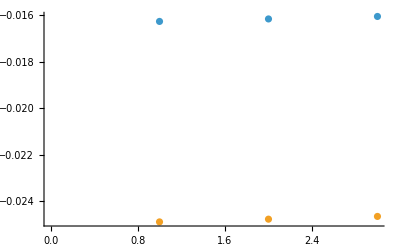

```mathematica
rig=7;
step=1;
polno=5;
{(StepsAllStepwise[[rig,-step]][[1;;3,2]][[All,1,polno]]//Values),(StepsAllStepwise[[rig,-step]][[1;;3,2]][[All,-1,polno]]//Values)}//ListPlot
```

```mathematica
{syts[[61]],syts[[65]],syts[[116]],syts[[137]],syts[[143]],syts[[161]],syts[[164]]}
```

{{{1,2,3,8},{4,6,7},{5,9}},{{1,2,3,8},{4,5,7},{6,9}},{{1,4,5,6},{2,7,8},{3,9}},{{1,2,6,8},{3,5,7},{4,9}},{{1,2,6,8},{3,4,7},{5,9}},{{1,4,5,7},{2,6,8},{3,9}},{{1,3,5,7},{2,6,8},{4,9}}}

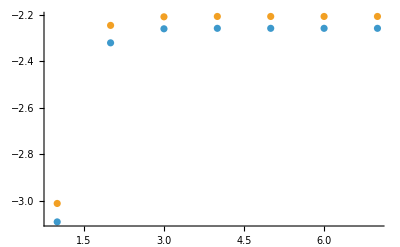

```mathematica
{(StepsAllStepwise[[161,-1]][[1;;3,2]][[All,All,1]]//Values)[[2]],(StepsAllStepwise[[164,-1]][[1;;3,2]][[All,All,1]]//Values)[[2]]}//ListPlot[#,PlotRange->All]&
```

```mathematica
startinterpord=3;
Λ0=3;
step=0.5;
interpord=3; 
test=SolutionFromSYTUptdStepwise[#]&/@syts[[1;;3]];
```

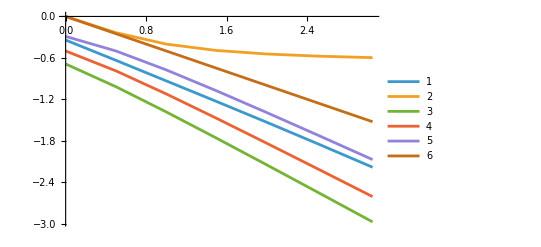

```mathematica
rig=3;
Show[Table[{test[[rig,-step]][[1]],test[[rig,-step]][[2]][[All,1]]//Values}//Transpose,{step,1,Length@(test[[rig]]),1}]//ListLinePlot[#,PlotLegends->Range[Length@(test[[rig]])]]&]
```

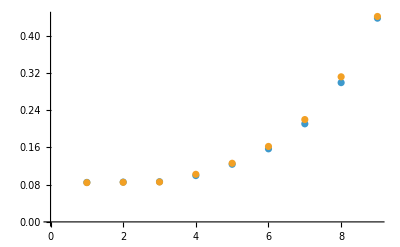

c[0,2,1]→-9.36518×10^-17-0.0053155/Λ^3-(1.42257×10^-16)/Λ^2+0.259259/Λ

{0.0005047720263867897150564790403850254327,0.0005238004555075085747696602354990709794,0.0005436813938485995848614328654266848339}

```mathematica
step=1;
polno=5;
{(StepsStepwise[[-step]][[1;;,2]][[All,1,polno]]//Values),(StepsStepwise[[-step]][[1;;,2]][[All,-1,polno]]//Values)}//ListPlot
ftransitUptdInterimFM[[polno]]
(StepsStepwise[[-step]][[1;;3,2]][[All,1,polno]]//Values)-(StepsStepwise[[-step]][[1;;3,2]][[All,-1,polno]]//Values)
```

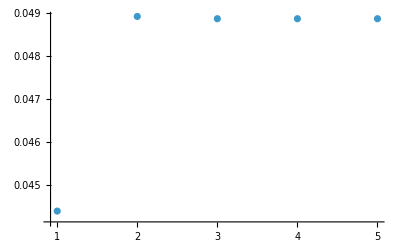

```mathematica
(StepsStepwise[[-step]][[All,2]][[All,All,polno]]//Values)[[1]]//ListPlot[#,PlotRange->All]&
```

```mathematica
Length/@StepsStepwise[[-1]][[All,2]]
```

{5,5,5,5,5,5,5,6,5}

```mathematica
a=1;
Round[test[[All,-1,3,-1]],10^-3]//N//Length
Round[test[[All,-1,3,-1]],10^-3]//N//DeleteDuplicates//Length

repeats=If[#[[2]]>1,{#[[1]]//Flatten,Position[Round[test[[All,-1,3,-1,a]],10^-3]//N,#[[1]]]//Flatten},Nothing]&/@Tally[Round[test[[All,-1,3,-1,a]],10^-3]//N];
repeatlist=repeats[[All,2]]

showSYT/@ToSYT/@rigs[[#]]&/@repeatlist
```

3

3

{}

{}

```mathematica
startinterpord=3;
Λ0=2;
step=0.5;
interpord=3;
testind=SolutionFromSYTUptdStepwise[syts[[10]]];
```

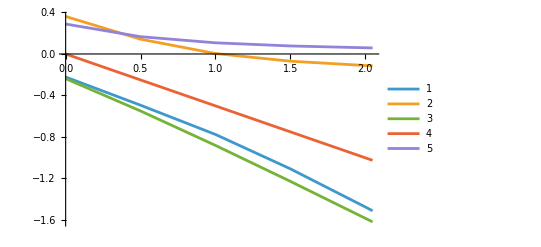

```mathematica
Show[Table[{testind[[-step]][[1]],testind[[-step]][[2]][[All,1]]//Values}//Transpose,{step,1,Length@(testind),1}]//ListLinePlot[#,PlotRange->All,PlotLegends->Range[Length@(testind)]]&]
```

```mathematica
interpfunc[xdata_,ydata_,interpord_,x_]:=
Sum[ydata[[-j]]*Product[If[j==j2,1,(x-xdata[[-j2]])/(xdata[[-j]]-xdata[[-j2]])],{j2,interpord}],{j,interpord}];
```

```mathematica
polno=2;
steps=4;
Manipulate[
xtest=testind[[-steps,1,1;;lastpoint]];
ytest=testind[[-steps,2,1;;lastpoint,polno]]//Values;
maninterp={#,interpfunc[xtest,ytest,interpord,#]}&/@Range[0,testind[[-steps,1,lastpoint]]-0.2,0.1];
(*interp={#,Interpolation[{xtest,ytest}//Transpose][#]}&/@Range[0,testind[[-steps,1,lastpoint+1]],0.1]//Quiet;
interpol={#,InterpolatingPolynomial[{xtest,ytest}//Transpose,#]}&/@Range[0,testind[[-steps,1,lastpoint+1]],0.1]//Quiet;*)
Show[{maninterp}//ListLinePlot[#,PlotStyle->Red]&,({testind[[-steps,1]],testind[[-steps,2,All,polno]]//Values}//Transpose)//ListPlot[#]&,PlotRange->All],
{lastpoint,4,Length@(testind[[-steps,1]])-1,1},
{{interpord,4},1,lastpoint,1},{polno,1,Length@(testind[[-steps,2]]),1},{steps,1,Length@testind,1}]
```

Part::partd: Part specification testind⟦-1,1,1;;4⟧ is longer than depth of object.

Part::partd: Part specification testind⟦-1,2,1;;4,1⟧ is longer than depth of object.

Values::invrl: The argument testind⟦-1,2,1;;4,1⟧ is not a valid Association or a list of rules.

Part::partd: Part specification testind⟦-1,1,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Range::range: Range specification in Range[0,-0.2+testind⟦-1,1,4⟧,0.1] does not have appropriate bounds.

Range::range: Range specification in Range[interpfunc[testind⟦-1,1,1;;4⟧,Values[testind⟦-1,2,1;;4,1⟧],4,0],interpfunc[testind⟦-1,1,1;;4⟧,Values[testind⟦-1,2,1;;4,1⟧],4,-0.2+testind⟦-1,1,4⟧],interpfunc[testind⟦-1,1,1;;4⟧,Values[testind⟦-1,2,1;;4,1⟧],4,0.1]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Values::invrl: The argument testind⟦-1,2,All,1⟧ is not a valid Association or a list of rules.